# Determination of α, β by fitting σ_R to ϵ at Q^2= 1.75 (GeV)^2

R^2/τ =A

2/R= B

2R/τ= X

R/τ= L

G_M^2 = G

σ_R = (G_M)^2 [1 + ϵ A + (B + ϵ X)[α1 (ϵ - 1) + α2 (ϵ^2 - 1)] + [B {1 -( 2 R ϵ/(1 + ϵ))} + 2 ϵ (1 + D)] [β1 (ϵ - 1) + β2 (ϵ^2 - 1)] ]

## Qattan Parameterization

```mathematica
epsdata={0.25,0.704,0.95}; 
sigmaRdata={0.030975216,0.034146765,0.035347878};
data=Transpose[{epsdata,sigmaRdata}]
A=0.162090081
B=7.04475
X=1.141884098
L=0.570942049
G=0.076436952
R=0.283899358

sigmaR=G*(1+(eps*A) +((B+(eps*X))*(alpha1*(eps-1)+alpha2*(eps^2-1)))+(B*(1-((eps*2*R)/(1+eps)))+ 2*eps*(1+L))*(beta1*(eps-1)+beta2*(eps^2-1)))
FindFit[data, {sigmaR},{alpha1,alpha2,beta1,beta2},eps]
```

{{0.25,0.0309752},{0.704,0.0341468},{0.95,0.0353479}}

0.16209

7.04475

1.14188

0.570942

0.076437

0.283899

0.076437 (1+0.16209 eps+(7.04475+1.14188 eps) (alpha1 (-1+eps)+alpha2 (-1+eps^2))+(beta1 (-1+eps)+beta2 (-1+eps^2)) (3.14188 eps+7.04475 (1-(0.567799 eps)/(1+eps))))

{alpha1→-17.3349,alpha2→-22.0152,beta1→19.2974,beta2→22.0729}

## Y_E and Y_ 3 Determination with Plot

### α values :

```mathematica
alpha1=-17.334895383089826
alpha2=-22.015227909294595
alpha0=-(alpha1+alpha2)
```

-17.3349

-22.0152

39.3501

### β values :

```mathematica
beta1=19.297373136210705
beta2=22.07287295563157
beta0=-(beta1+beta2)
```

19.2974

22.0729

-41.3702

### Y_E , Y_ 3 & Y_M :

39.3501-17.3349 eps-22.0152 eps^2

-41.3702+19.2974 eps+22.0729 eps^2

3.52237 (39.3501-17.3349 eps-22.0152 eps^2+(-41.3702+19.2974 eps+22.0729 eps^2) (1-(0.567799 eps)/(1+eps)))

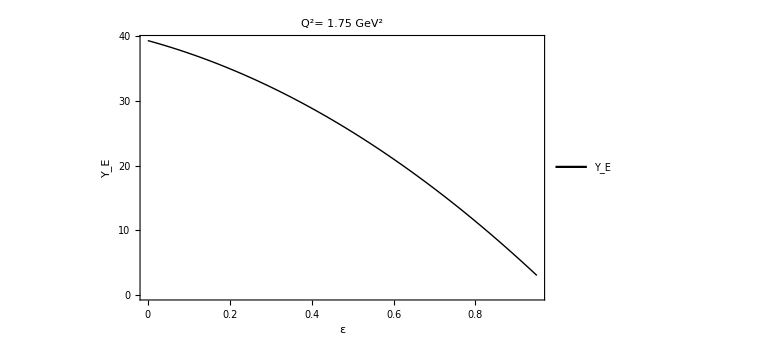

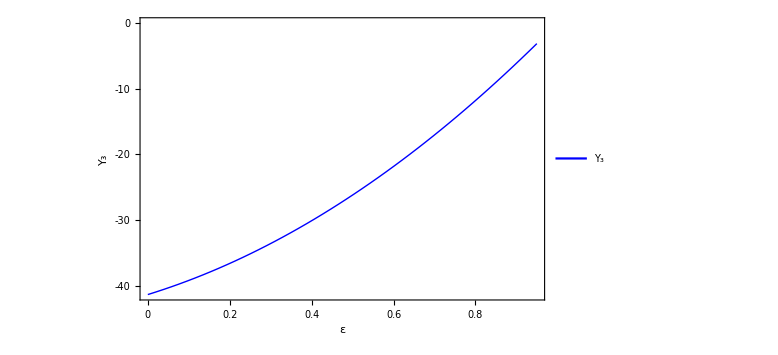

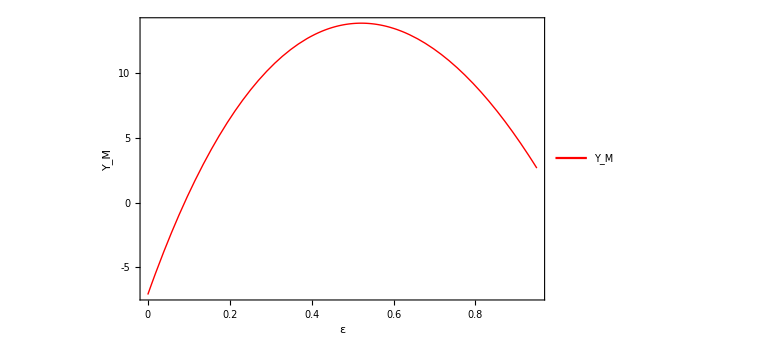

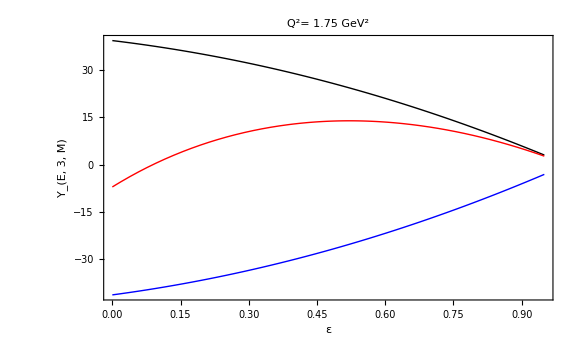

```mathematica
YE=39.350123292384424-(17.334895383089826*eps)-(22.015227909294595*eps^2)
Y3=-41.370246091842276+(19.297373136210705*eps)+(22.07287295563157*eps^2)
YM=(YE+(1-R*(2*eps/(1+eps)))*Y3)/R
YEplot=Plot[YE, {eps,0,0.95},PlotStyle->{Black,Thick},FrameLabel->{Style["ε",Bold,16],Style["Y_E",Bold,16]},PlotLegends-> Placed[LineLegend[{"Y_E"},LabelStyle->Directive[22]],{0.92,0.8}], Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2= 1.75 GeV^2",Bold,24], ImageSize-> Large]
Y3plot=Plot[Y3, {eps,0,0.95},PlotStyle->{Blue,Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_3",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_3"},LabelStyle->Directive[22]],{0.92,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]
YMplot=Plot[YM, {eps,0,0.95},PlotStyle->{Red, Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_M"},LabelStyle->Directive[22]],{0.92,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]

Show[YEplot,Y3plot,YMplot, PlotRange->All,FrameLabel->{Style["ε",Bold,26],Style["Y_(E, 3, M)  ",Bold,24]},Frame-> True,FrameTicks->All,FrameTicksStyle-> Directive[Black,12],ImageSize-> Large]
```

## My PT fit

```mathematica
Q2=1.75
fcmuR=1+(-0.11723721716472688)*Q2+(0.0025226146422440594)*(Q2)^2+(-0.0004347472619650877)*(Q2)^3
fcR=fcmuR/2.7972
```

1.75

0.80023

0.286083

```mathematica
epsdata={0.25,0.704,0.95}; 
sigmaRdata={0.030975216,0.034146765,0.035347878};
data=Transpose[{epsdata,sigmaRdata}]
Afc=0.16544318
Bfc=6.972995264
Xfc=1.15363
Lfc=0.57682
Gfc=0.076217035
Rfc=0.2860826554041564

sigmaRfc=Gfc*(1+(eps*Afc) +((Bfc+(eps*Xfc))*(alpha1fc*(eps-1)+alpha2fc*(eps^2-1)))+(Bfc*(1-((eps*2*Rfc)/(1+eps)))+ 2*eps*(1+Lfc))*(beta1fc*(eps-1)+beta2fc*(eps^2-1)))
FindFit[data, {sigmaRfc},{alpha1fc,alpha2fc,beta1fc,beta2fc},eps]
```

{{0.25,0.0309752},{0.704,0.0341468},{0.95,0.0353479}}

0.165443

6.973

1.15363

0.57682

0.076217

0.286083

0.076217 (1+0.165443 eps+(6.973+1.15363 eps) (alpha1fc (-1+eps)+alpha2fc (-1+eps^2))+(beta1fc (-1+eps)+beta2fc (-1+eps^2)) (3.15364 eps+6.973 (1-(0.572165 eps)/(1+eps))))

{alpha1fc→-17.3465,alpha2fc→-22.1608,beta1fc→19.3798,beta2fc→22.1734}

```mathematica
alpha1fc=-17.346493500405852
alpha2fc=-22.160842493878633
alpha0fc=-(alpha1fc+alpha2fc)
```

-17.3465

-22.1608

39.5073

```mathematica
beta1fc=19.379827469502313
beta2fc=22.17336076306499
beta0fc=-(beta1fc+beta2fc)
```

19.3798

22.1734

-41.5532

39.5073-17.3465 eps-22.1608 eps^2

-41.5532+19.3798 eps+22.1734 eps^2

3.49549 (39.5073-17.3465 eps-22.1608 eps^2+(-41.5532+19.3798 eps+22.1734 eps^2) (1-(0.572165 eps)/(1+eps)))

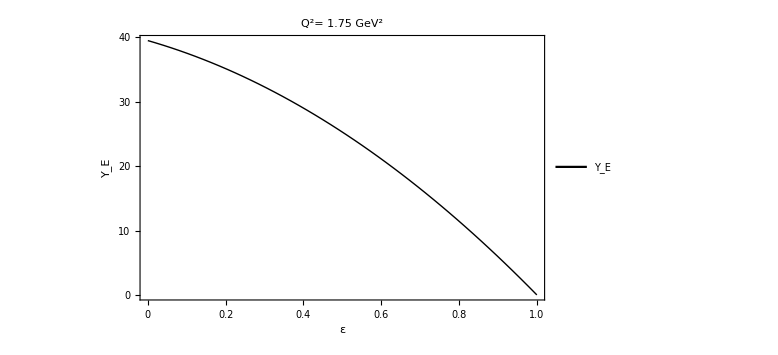

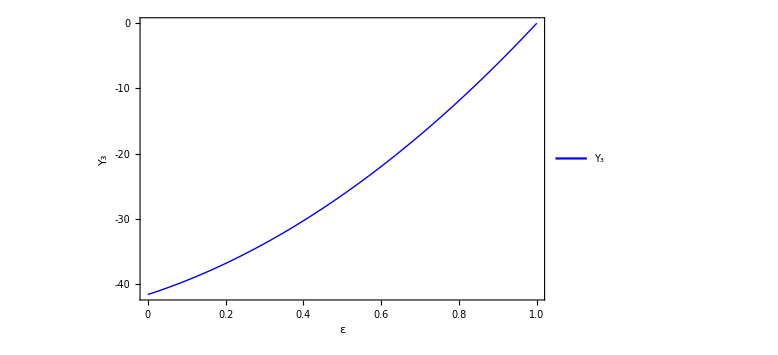

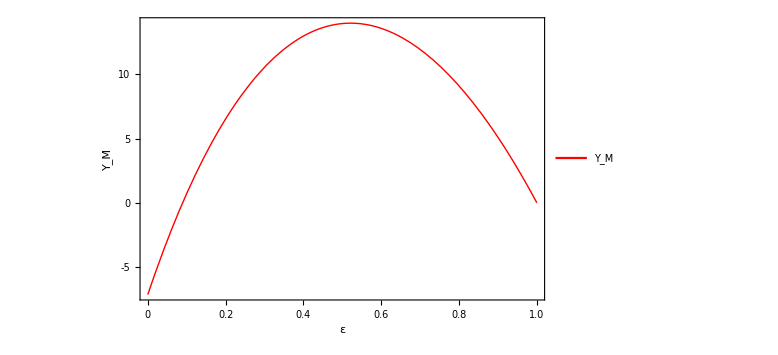

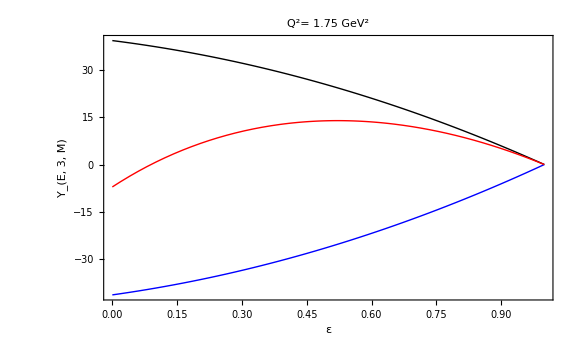

```mathematica
YEfc=39.50733599428449+(-17.346493500405852*eps)+(-22.160842493878633*eps^2)
Y3fc=-41.55318823256731+(19.379827469502313*eps)+(22.17336076306499*eps^2)
YMfc=(YEfc+(1-Rfc*(2*eps/(1+eps)))*Y3fc)/Rfc
YEplotfc=Plot[YEfc, {eps,0,1},PlotStyle->{Black,Thick},FrameLabel->{Style["ε",Bold,16],Style["Y_E",Bold,16]},PlotLegends-> Placed[LineLegend[{"Y_E"},LabelStyle->Directive[22]],{0.9,0.8}], Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2= 1.75 GeV^2",Bold,24], ImageSize-> Large]
Y3plotfc=Plot[Y3fc, {eps,0,1},PlotStyle->{Blue,Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_3",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_3"},LabelStyle->Directive[22]],{0.9,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]
YMplotfc=Plot[YMfc, {eps,0,1},PlotStyle->{Red, Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_M"},LabelStyle->Directive[22]],{0.9,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]

Show[YEplotfc,Y3plotfc,YMplotfc,PlotRange->All,FrameLabel->{Style["ε",Bold,26],Style["Y_(E, 3, M)  ",Bold,24]},Frame-> True,FrameTicks->All,FrameTicksStyle-> Directive[Black,14],ImageSize-> Large]
```